# CS 478

## Scott Leland Crossen

## Nearest Neighbor Project

### Part 1

The code that implements the knn nearest neighbor algorithm is included with the submission of this project. It is written in Scala and follows the functional paradigm. Immutability is observed in all but the underlying learner. Optional distance weighting is included as well.

### Part 2

For this section please note that I had to use non-conventional approximation methods to compute the large amount of data for the magic telescope problem in a reasonable amount of time. This could lead to a graph solution that looks different than the TA’s solution. Accuracy showed a maximum around k~14 neighbors. For the most part, normalization did improve accuracy -- but not by much. Accuracy for normalized k=3 was around .792. Accuracy for unnormalized data was around .742. What is interesting, however, is the fact that the normalized data set reached it’s optimal value quicker than the unnormalized data set.

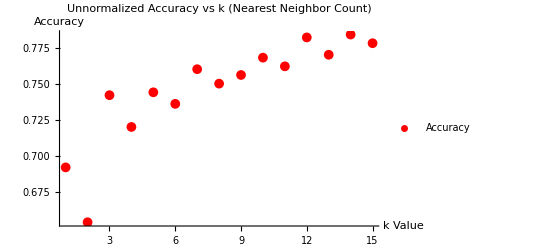

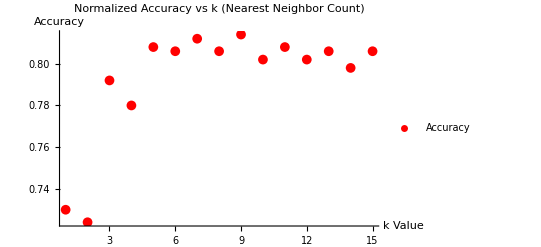

```mathematica
data={0.692,0.654,0.742,0.72,0.744,0.736,0.76,0.75,0.756,0.768,0.762,0.782,0.77,0.784,0.778};
ListPlot[Transpose[{Range[15] ,data}],AxesLabel->{Style["k Value", Black],Style["Accuracy", Black]}, PlotLabel->Style["Unnormalized Accuracy vs k (Nearest Neighbor Count)", Black], 
PlotStyle->{Blue, Red},PlotMarkers-> {●,10}, PlotLegends->{"Accuracy"}, PlotRange->All]
data={0.73,0.724,0.792,0.78,0.808,0.806,0.812,0.806,0.814,0.802,0.808,0.802,0.806,0.798,0.806};
ListPlot[Transpose[{Range[15] ,data}],AxesLabel->{Style["k Value", Black],Style["Accuracy", Black]}, PlotLabel->Style["Normalized Accuracy vs k (Nearest Neighbor Count)", Black], PlotStyle->{Blue, Red},PlotMarkers-> {●,10}, PlotLegends->{"Accuracy"}, PlotRange->All]
```

### Part 3

With odd values of k and distance weighting, the following plot was produced for the mean-squared-error of the housing data. This shows a relative max at around k=7. One interesting behavior of this data is the rather odd discontinuity right before the lowest mean-squared-error is reached. I’m not sure why this is, but perhaps it’s because of the clustered nature of the data with clusters of size 7-8. Another interesting feature of this data is the fact that it appears to asymptote toward a MSE of 6.0. At this point the data is homogenous enough between neighbors.

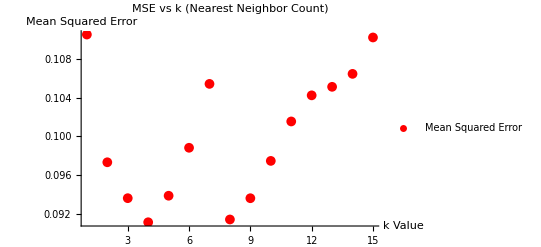

```mathematica
data={0.11048209369313852,0.0973422647088986,0.09364829522013853,0.09117181500132987,0.09390017799877275,0.09883379397903759,0.10540618956667139,0.09145729298073783,0.09364383035816154,0.09748352571793637,0.10154165547436601,0.1042274951595853,0.10510462401329672,0.10643729037812187,0.11018220486168717};
ListPlot[Transpose[{Range[15],data}],AxesLabel->{Style["k Value", Black],Style["Mean Squared Error", Black]}, PlotLabel->Style["MSE vs k (Nearest Neighbor Count)", Black], PlotStyle->{Blue, Red},PlotMarkers-> {●,10}, PlotLegends->{"Mean Squared Error"}, PlotRange->All]
```

### Part 4

The above experiment was repeated for the magic-telescope project and the housing problem except this time with weighted distances used. The results indicate the same relative maximum around k=14. The overall accuracy is an increase over the initial tests and goes to show that distance weighting does help in some respect, but not much. The nearest-neighbor optimum did not change. As before, the magic telescope problem had a best-k value around 14. The housing had a best k-value around 8.

The first plot is the magic-telescope problem. The second is the Housing problem.

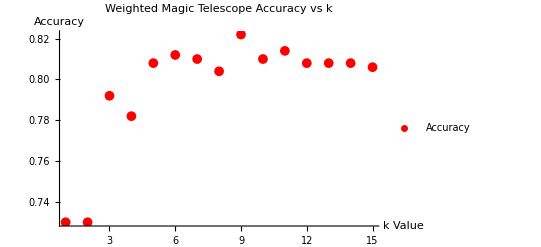

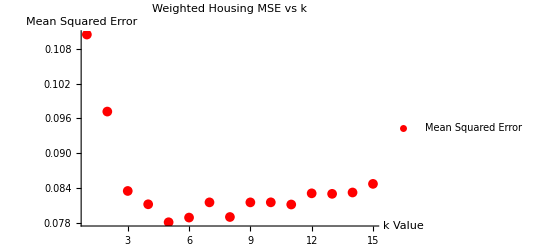

```mathematica
data={0.73,0.73,0.792,0.782,0.808,0.812,0.81,0.804,0.822,0.81,0.814,0.808,0.808,0.808,0.806};
ListPlot[Transpose[{Range[15] ,data}],AxesLabel->{Style["k Value", Black],Style["Accuracy", Black]}, PlotLabel->Style["Weighted Magic Telescope Accuracy vs k", Black], PlotStyle->{Blue, Red},PlotMarkers-> {●,10}, PlotLegends->{"Accuracy"}, PlotRange->All]
data={0.1104820936931385,0.09717836231539492,0.08346447793939876,0.0811652802293374,0.0780600875014959,0.07886876541845707,0.081495962414472,0.07896719906243962,0.08149318252523417,0.08150113185271168,0.08112563857165131,0.08305547229484354,0.08296852799942477,0.08320057300725948,0.08468968316393786};
ListPlot[Transpose[{Range[15],data}],AxesLabel->{Style["k Value", Black],Style["Mean Squared Error", Black]}, PlotLabel->Style["Weighted Housing MSE vs k", Black], PlotStyle->{Blue, Red},PlotMarkers-> {●,10}, PlotLegends->{"Mean Squared Error"}, PlotRange->All]
```

### Part 5

The below plot shows the accuracy value plotted against k ranged between 1 and 15.

This section required a “categorical” distance metric. To do this, I created a helper function that would take the appropriate columns and compute a quasi-distance double from them. The algorithm is best described below:
1. When comparing two elements of a vector between a training row and a testing row, decompose each vector into elements and call an element-distance metric on them.
2. For quantitative features, use normal distances. For categorical features, compose a list of all other labels that have this same categorical value as the training feature.
3. Do the same with the testing feature
4. For each distinct label possible, count the number of occurrences in each list. Divide number of occurrences by the length of the list.
5. Call the normal distance function between the two resulting values. Sum all possible distances between labels.
6. Return the result.

For this dataset, values of k were iteratively used starting with 1. Eventually (because it was taking a while to compute) I stopped the calculation short of 15 and displayed the results. Seen as only one k-value was requested, this shouldn’t be a problem. A 85/15 split of the data was used between training and testing sets.

As you can see, the desired accuracy of 70-80% was achieved.

As before, it is odd that accuracy decreases as k increases. Perhaps this can be attributed to the fact that the data-set is very singular and doesn’t have many groupings. This fact can be corroborated with the apparent 100% accuracy for a k=1 value. This means that data is obviously duplicated in the data set. Every neighbor that is added then just weakens the hold that the duplicate data has on the testing feature.

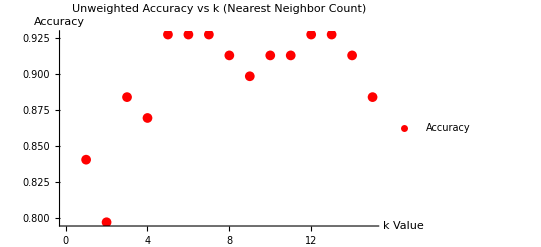

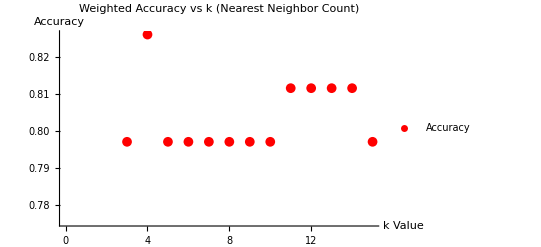

```mathematica
data={0.8405797101449275,0.7971014492753623,0.8840579710144928,0.8695652173913043,0.927536231884058,0.927536231884058,0.927536231884058,0.9130434782608695,0.8985507246376812,0.9130434782608695,0.9130434782608695,0.927536231884058,0.927536231884058,0.9130434782608695,0.8840579710144928};
ListPlot[Transpose[{Range[15],data}],AxesLabel->{Style["k Value", Black],Style["Accuracy", Black]}, PlotLabel->Style["Unweighted Accuracy vs k (Nearest Neighbor Count)", Black], PlotStyle->{Blue, Red},PlotMarkers-> {●,10}, PlotLegends->{"Accuracy"}]
data={0.7536231884057971,0.7536231884057971,0.7971014492753623,0.8260869565217391,0.7971014492753623,0.7971014492753623,0.7971014492753623,0.7971014492753623,0.7971014492753623,0.7971014492753623,0.8115942028985508,0.8115942028985508,0.8115942028985508,0.8115942028985508,0.7971014492753623};
ListPlot[Transpose[{Range[15],data}],AxesLabel->{Style["k Value", Black],Style["Accuracy", Black]}, PlotLabel->Style["Weighted Accuracy vs k (Nearest Neighbor Count)", Black], PlotStyle->{Blue, Red},PlotMarkers-> {●,10}, PlotLegends->{"Accuracy"}]
```

### Part 6

For this section I wrote a divide-and-conquer pruning algorithm. The algorithm would partition the testing set into n partitions where n is set by the user. Each partition would then be iteratively removed from the data set and (n-1)-fold cross validation would be used on the remaining testing set to judge new accuracy. The partition that received the best accuracy would then recursively call the partitioning function on the best-scored removed-scored subset. The overall subset would be added back to the original set, but each child partition would be iterated over and sequentially removed and the accuracy of the overall test re-gauged recursively. Eventually a base-case would be reached when there was one feature left. The worst-scoring feature would be removed from the testing set if it improved accuracy. This whole process is then repeated until accuracy does not improve.

Below is a plot of accuracy on the housing-price data set. The x-axis represents the divide-and-conquer splitting factor. 2 means the data was split in half at each step, 3 means it was split in thirds, etc. The y axis represents the resulting mean-squared-error of the testing data. Notice that although overall performance is increased when reduction is used but the splitting factor does not matter. The resulting MSE difference appears to just be noise in the data.

For this experiment, k was set at 6 and distance-weighting was used to reduce mean-squared-error.

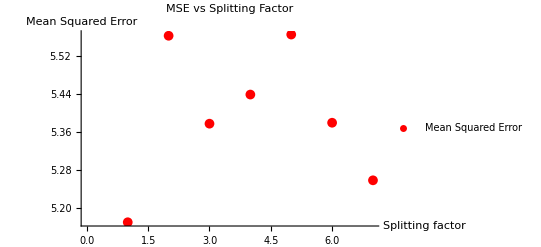

```mathematica
data={5.170726335826066,5.561567758100842,5.377307054302036,5.438346722647866,5.564109839958595,5.379284607312965,5.258637715316816};
ListPlot[Transpose[{Range[7],data}],AxesLabel->{Style["Splitting factor", Black],Style["Mean Squared Error", Black]}, PlotLabel->Style["MSE vs Splitting Factor", Black], PlotStyle->{Blue, Red},PlotMarkers-> {●,10}, PlotLegends->{"Mean Squared Error"}]
```